```mathematica
sol=DSolve[{x'[t]==y[t], y'[t]==x[t],x[0]==2,y[0]==0},{x[t],y[t]},t]
```

{{x[t]→ⅇ^-t (1+ⅇ^(2 t)),y[t]→ⅇ^-t (-1+ⅇ^(2 t))}}

```mathematica
fun = Table[sol[[1]][[i]][[2]],{i,1,Length[sol[[1]]]}];
```

```mathematica
euler=ReadList["D:\\VisualStdudio\\calculatem\\calculation-methods-labs\\lab6\\lab6\\output.txt",Number,RecordLists->True];
```

```mathematica
tau = 0.1;T=1;
```

```mathematica
timetable = Table[i,{i,0,T,tau}];
```

```mathematica
n = Length[euler[[1]]];
```

```mathematica
dots = Table[euler[[All,i]],{i,1,n}]
```

{{2,2.0202,2.06101,2.12306,2.20717,2.31443,2.44615,2.60391,2.78956,3.00527,3.25352},{0,0.20202,0.408122,0.620427,0.841144,1.07259,1.3172,1.57759,1.85655,2.15708,2.48243}}

```mathematica
points = Table[Table[{timetable[[j]],dots[[i]][[j]]},{j,1,Length[timetable]}],{i,1,n}];
```

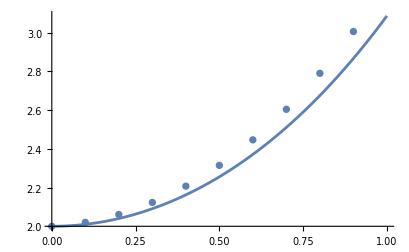
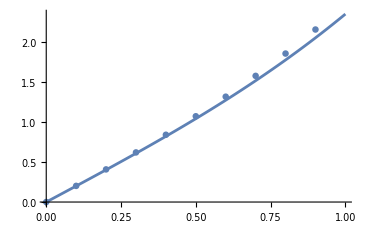

```mathematica
Paints = Table[Show[Plot[fun[[i]],{t,0,T}], ListPlot[points[[i]]]],{i,1,n}]
```